```mathematica
<<KerrGeodesics`
<<SpinWeightedSpheroidalHarmonics`
```

```mathematica
dtdλ[M_,a_,r_,ℰ_,ℒ_,θ_] := ℰ(((r^2+a^2)^2)/(r^2-2 M r+a^2)-a^2 Sin[θ]^2)+a ℒ(1-(r^2+a^2)/(r^2-2M r+a^2));
gtt[M_,a_,r_,θ_] := -(a^4+2 r^4+a^2 r (2 M+3 r)+a^2 (a^2+r (-2 M+r)) Cos[2 θ])/((a^2+r (-2 M+r)) (a^2+2 r^2+a^2 Cos[2 θ]));
gtϕ[M_,a_,r_,θ_]:=-(4 a M r)/((a^2+r (-2 M+r)) (a^2+2 r^2+a^2 Cos[2 θ]));
ut[M_,a_,r_,ℰ_,ℒ_,θ_] := gtϕ[M,a,r,θ] ℒ- gtt[M,a,r,θ] ℰ;
```

```mathematica
SourceNonZero[l_,m_,k_,M_,a_,r0_,xi_]:=Module[
{ly=l,my=m,ky=k,My=M,ay=a,r0y=r0,xiy=xi,Δ,ℰ,ℒ,𝒬,Ωθ,Ωϕ,Υ,λ,Freqs,tp,rp,θp,ϕp,orbit,Integrand,Ans,S},

orbit = KerrGeoOrbit[ay,r0y,0,xiy];
{tp,rp,θp,ϕp}=orbit["Trajectory"];

Δ=r0y^2-2My r0y + ay^2;

ℰ=orbit["Energy"];
ℒ=orbit["AngularMomentum"];
Υ =orbit["Frequencies"]["Υ_θ"];

Freqs = KerrGeoFrequencies[ay,r0y,0,xiy];
Ωθ = Freqs[[2]];
Ωϕ = Freqs[[3]];

S=SpinWeightedSpheroidalHarmonicS[0,ly,my,ay (m Ωϕ-k Ωθ)];
Integrand:=S[θp[λ],0]/ut[My,ay,r0y,ℰ,ℒ,θp[λ]] Cos[((m Ωϕ-k Ωθ) tp[λ]-my ϕp[λ])]dtdλ[My,ay,r0y,ℰ,ℒ,θp[λ]];


Ans=-(Ωθ r0y)/Δ NIntegrate[Integrand,{λ,0,(2π)/Υ},Method->"Trapezoidal",PrecisionGoal->30(*,MaxRecursion->30*)];

Ans
]
Source[l_,m_,k_,M_,a_,r0_,xi_]:=If[Mod[l+m+k,2]==1,0,SourceNonZero[l,m,k,M,a,r0,xi]];
```

```mathematica
l=3;
m=-1;
knum=20;
data =Table[SourceNonZero[l,m,k,1`32,.998`32,10`32,Cos[π/4`32]],(*{l,0,5},{m,-l,l},*){k,-knum,knum}];
```

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in λ$39565601 in the region {{0.,1.78664}}. NIntegrate obtained -1.59395×10^-14 and 4.12951×10^-15 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in λ$39594384 in the region {{0.,1.78664}}. NIntegrate obtained 8.09379×10^-15 and 1.76985×10^-15 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in λ$39623169 in the region {{0.,1.78664}}. NIntegrate obtained -1.27853×10^-14 and 1.04842×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvi will be suppressed during this calculation.

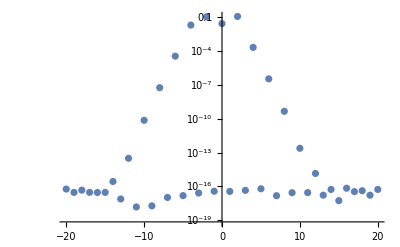

```mathematica
ListLogPlot[Thread[{Table[k,{k,-knum,knum}],Abs[data]}],GridLines->{Table[n,{n,-20,20}],Table[10^-n,{n,0,18}]}]
```